# Homework 4

## Marvyn Bailly

## Question 1

### Part a

```mathematica
Clear[A,t]
f[t_,A_] := -A^5*Sin[t]^5;
y1[t_] := Cos[t];
y2[t_] := Sin[t];
yp[t_,A_] = -y1[t]*Integrate[y2[t]*f[t,A]/Wronskian[{y1[t],y2[t]},t],t]+y2[t]*Integrate[y1[t]*f[t,A]/Wronskian[{y1[t],y2[t]},t],t]

yReg = A*Sin[t]+ϵ*yp[t,A];
yRegPlot[t_,A_] = yReg;

(*FullSimplify[yp[t,A]]
DSolve[{y''[t]+y[t]==-A^5*Sin[t]^5,y[0]==0,y'[0]==0},y[t],t] // FullSimplify

yReg[t_,A_] = A*Sin[t]+ϵ*yp[t,A]
*)
```

-1/6 A^5 Sin[t]^7+A^5 Cos[t] ((5 t)/16-15/64 Sin[2 t]+3/64 Sin[4 t]-1/192 Sin[6 t])

```mathematica
Manipulate[Plot[yReg[t,A],{t,0,20}],{A,0.1,5}]
```

### Part c

```mathematica
DSolve[{y''[t]+y[t]==0,y[0]==0,y'[0]==A},y[t],t]
```

{{y[t]→A Sin[t]}}

```mathematica
Clear[A,t,f,y1,y2,ϵ,yp]
f[t_,A_] := -A^5*Sin[t]^5 + 5/8*A^5*Sin[t];
y1[t_] := Cos[t];
y2[t_] := Sin[t];
yp[t_,A_] = -y1[t]*Integrate[y2[t]*f[t,A]/Wronskian[{y1[t],y2[t]},t],t]+y2[t]*Integrate[y1[t]*f[t,A]/Wronskian[{y1[t],y2[t]},t],t]

yPoin = A*Sin[(1+ϵ*5/16*A^4)t]+ϵ*yp[(1+ϵ*5/16*A^4)t,A]
yPoinPlot[t_,A_] = yPoin;

FullSimplify[yPoinPlot[t,A]]
DSolve[{y''[t]+y[t]==f[t,A],y[0]==0,y'[0]==-5/16*A^5},y[t],t] // FullSimplify
```

Sin[t] (-5/16 A^5 Cos[t]^2-1/6 A^5 Sin[t]^6)-Cos[t] (5/64 A^5 Sin[2 t]-3/64 A^5 Sin[4 t]+1/192 A^5 Sin[6 t])

A Sin[t (1+(5 A^4 ϵ)/16)]+ϵ (Sin[t (1+(5 A^4 ϵ)/16)] (-5/16 A^5 Cos[t (1+(5 A^4 ϵ)/16)]^2-1/6 A^5 Sin[t (1+(5 A^4 ϵ)/16)]^6)-Cos[t (1+(5 A^4 ϵ)/16)] (5/64 A^5 Sin[2 t (1+(5 A^4 ϵ)/16)]-3/64 A^5 Sin[4 t (1+(5 A^4 ϵ)/16)]+1/192 A^5 Sin[6 t (1+(5 A^4 ϵ)/16)]))

1/192 A (192-47 A^4 ϵ+A^4 ϵ (-14 Cos[t (2+(5 A^4 ϵ)/8)]+Cos[t (4+(5 A^4 ϵ)/4)])) Sin[t+5/16 A^4 t ϵ]

{{y[t]→1/384 A^5 (-80 Sin[t]-15 Sin[3 t]+Sin[5 t])}}

#### Part D

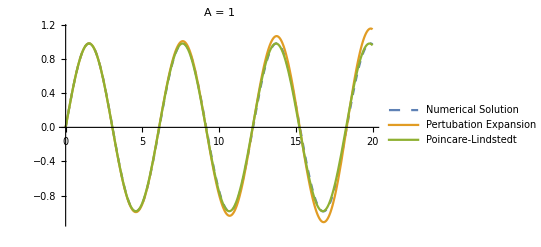

```mathematica
ϵ=0.1;
A=1;
solution =NDSolve[{y''[t]+y[t]+ϵ*y[t]^5==0,y[0]==0,y'[0]==A},y[t],{t,0,20}];
	
Plot[{Evaluate[y[t] /. solution],yRegPlot[t,A],yPoinPlot[t,A]},{t,0,20},PlotStyle->{Dashed,Line,Line},PlotLabel->"A = "<>ToString[A],PlotLegends->{"Numerical Solution","Pertubation Expansion","Poincare-Lindstedt "}]
```

## Question 2

#### Part A

```mathematica
Clear[A,B,t,T]
u[t,τ] = A[τ]*Cos[t]+B[τ]*Sin[t];
Expand[(D[u[t,τ],t])^3]
```

B[τ]^3 Cos[t]^3-3 A[τ] B[τ]^2 Cos[t]^2 Sin[t]+3 A[τ]^2 B[τ] Cos[t] Sin[t]^2-A[τ]^3 Sin[t]^3

```mathematica
ρ = (4α^2)/(α^2+(4-α^2)*Exp[-t])
DSolve[{2A'[t]+1/4B[t]^3+1/4(ρ-B[t]^2)B[t]-B[t]==0},B[t],t] // FullSimplify
DSolve[{2B'[t]+1/4B[t]^3+1/4(ρ-B[t]^2)B[t]-B[t]==0, B[0]==A},B[t],t] // FullSimplify
```

(4 α^2)/(α^2+ⅇ^-t (4-α^2))

{{B[t]→-(2 (4+(-1+ⅇ^t) α^2) A'[t])/(-4+α^2)}}

{{B[t]→(2 A √(ⅇ^t (-4+α^2)))/(√(-4+α^2) √(4+(-1+ⅇ^t) α^2))}}

#### Part B

```mathematica
DSolve[{y''[t]+y[t]==2Cos[t]-8/3Cos[t]^3,y[0]==0,y'[0]==A},y[t],t] // TrigReduce
```

{{y[t]→1/12 (-Cos[t]+Cos[3 t]+12 A Sin[t])}}

O(ϵ^2) terms

```mathematica
Clear[ϵ,ω]
ω[ϵ_] = Subscript[ω, 0]+ϵ*Subscript[ω, 1]+ϵ^2*Subscript[ω, 2]
y[ϵ_,τ_] = Subscript[y, 0][τ] + ϵ*Subscript[y, 1][τ]+ϵ^2*Subscript[y, 2][τ]
gross1[ϵ_,τ_]=ω[ϵ]^2*D[y[ϵ,τ],{τ,2}]+y[ϵ,τ]+ϵ(-ω[ϵ]*D[y[ϵ,τ],τ]+1/3*ω[ϵ]*(D[y[ϵ,τ],τ])^3)
Coefficient[Expand[gross1[ϵ,τ]],ϵ^1]
gross2[ϵ_,τ_]=Coefficient[Expand[gross1[ϵ,τ]],ϵ^2] /. {Subscript[ω, 0] -> 1, Subscript[ω, 1]->0}
```

ω_0+ϵ ω_1+ϵ^2 ω_2

y_0[τ]+ϵ y_1[τ]+ϵ^2 y_2[τ]

y_0[τ]+ϵ y_1[τ]+ϵ^2 y_2[τ]+ϵ ((-ω_0-ϵ ω_1-ϵ^2 ω_2) (y_0'[τ]+ϵ y_1'[τ]+ϵ^2 y_2'[τ])+1/3 (ω_0+ϵ ω_1+ϵ^2 ω_2) (y_0'[τ]+ϵ y_1'[τ]+ϵ^2 y_2'[τ])^3)+(ω_0+ϵ ω_1+ϵ^2 ω_2)^2 (y_0''[τ]+ϵ y_1''[τ]+ϵ^2 y_2''[τ])

y_1[τ]-ω_0 y_0'[τ]+1/3 ω_0 y_0'[τ]^3+2 ω_0 ω_1 y_0''[τ]+ω_0^2 y_1''[τ]

y_2[τ]-y_1'[τ]+y_0'[τ]^2 y_1'[τ]+2 ω_2 y_0''[τ]+y_2''[τ]

Plug stuff in

```mathematica
Subscript[y, 0][τ_]=2*Sin[τ];
Subscript[y, 1][τ_]=1/12 (-Cos[τ]+Cos[3 τ]+12 Subscript[α, 1] Sin[τ])
gross2[ϵ,τ]
```

1/12 (-Cos[τ]+Cos[3 τ]+12 Sin[τ] α_1)

1/12 (-Sin[τ]+3 Sin[3 τ]-12 Cos[τ] α_1)+1/3 Cos[τ]^2 (Sin[τ]-3 Sin[3 τ]+12 Cos[τ] α_1)-4 Sin[τ] ω_2+y_2[τ]+y_2''[τ]

Enforce <RHS,sin>=0 and <RHS,cos>=0

```mathematica
gross3[ϵ_,τ_]=TrigReduce[-(1/12 (-Sin[τ]+3 Sin[3 τ]-12 Cos[τ] Subscript[α, 1])+1/3 Cos[τ]^2 (Sin[τ]-3 Sin[3 τ]+12 Cos[τ] Subscript[α, 1])-4 Sin[τ] Subscript[ω, 2])]
Solve[{Integrate[gross3[ϵ,τ]*Sin[τ],{τ,0,2*Pi}]==0,Integrate[gross3[ϵ,τ]*Cos[τ],{τ,0,2*Pi}]==0},{Subscript[α, 1],Subscript[ω, 2]}]
```

1/12 (3 Sin[τ]+2 Sin[3 τ]+3 Sin[5 τ]-24 Cos[τ] α_1-12 Cos[3 τ] α_1+48 Sin[τ] ω_2)

{{α_1→0,ω_2→-1/16}}

```mathematica
Sin[0]
```

0

#### C

Plotting fun

```mathematica
Clear[A,ϵ,yPoin,solution]
ρ = (4A^2)/(A^2+(4-A^2)*Exp[-ϵ*t]);

yMulti[t_] = Sqrt[ρ]Sin[t]
yPoin[t_] = 2*Sin[(1-ϵ^2/16)*t]
```

2 √(A^2/(A^2+(4-A^2) ⅇ^(-t ϵ))) Sin[t]

2 Sin[t (1-ϵ^2/16)]

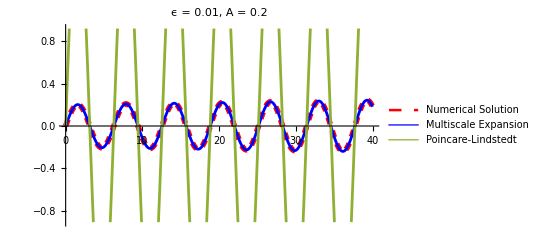

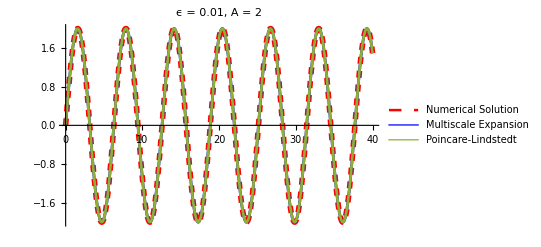

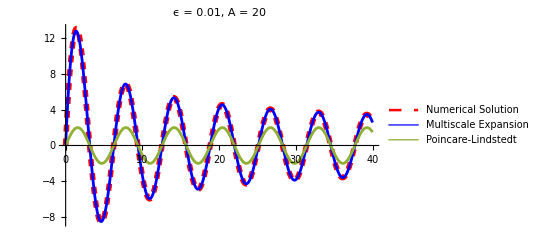

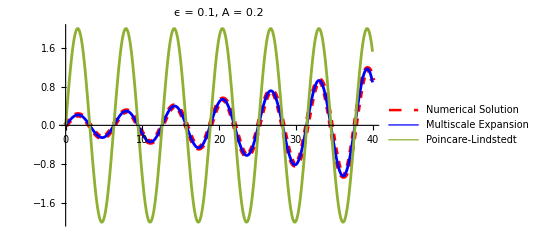

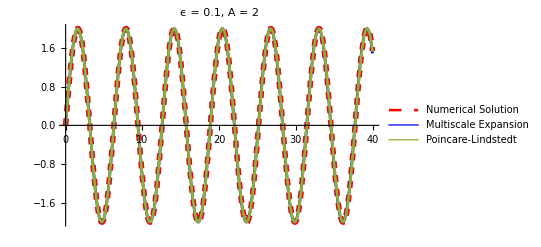

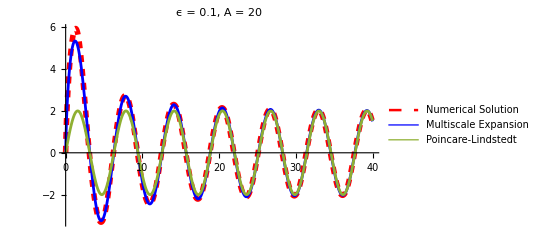

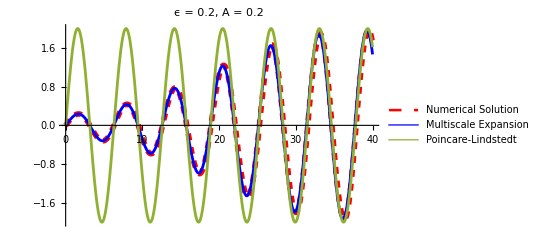

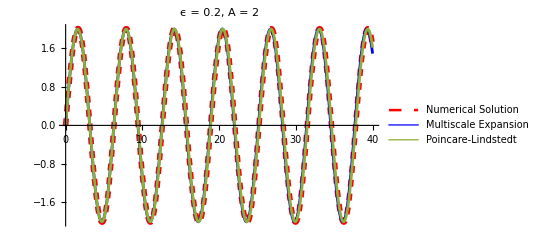

```mathematica
ϵList = {0.01,0.1,0.2,0.3};
AList = {.2,2,20};

For[i=1,i<5,i++,
	ϵ = ϵList[[i]];
	For[j=1,j<4,j++,
		A = AList[[j]];
		solution =NDSolve[{y''[t]+y[t]+ϵ*(-y'[t]+1/3*(y'[t])^3)==0,y[0]==0,y'[0]==A},y[t],{t,0,40}];
		Print[Plot[{Evaluate[y[t] /. solution],yMulti[t],yPoin[t]},{t,0,40},PlotStyle->{{Red,Dashed,Thickness[0.01]},{Blue,Line,Thickness[0.005]},{Line,Thickness[0.005]}},PlotLabel->"ϵ = "<>ToString[ϵ]<> ", A = "<>ToString[A],PlotLegends->{"Numerical Solution","Multiscale Expansion","Poincare-Lindstedt "}]]
	]
]
```

#### Part D

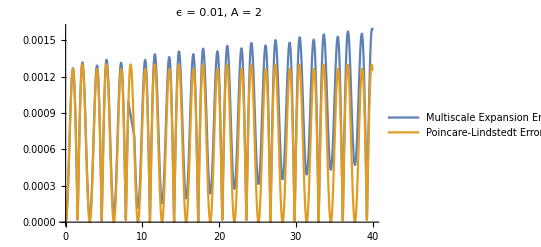

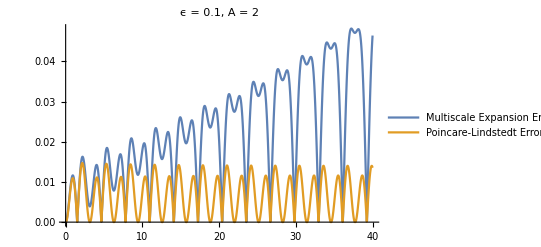

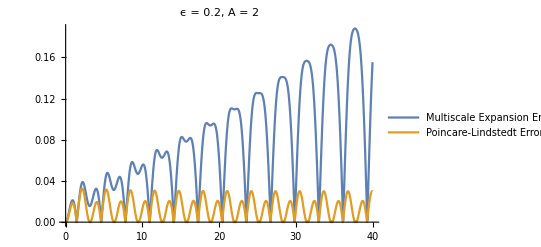

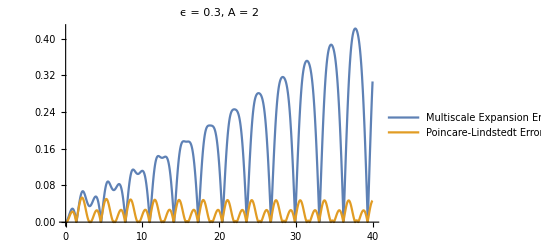

```mathematica
ϵList = {0.01,0.1,0.2,0.3};
A = 2;

For[i=1,i<5,i++,
	ϵ = ϵList[[i]];
	solution =NDSolve[{y''[t]+y[t]+ϵ*(-y'[t]+1/3*(y'[t])^3)==0,y[0]==0,y'[0]==A},y[t],{t,0,40}];
	Print[Plot[{Abs[Evaluate[y[t] /. solution]-yMulti[t]],Abs[Evaluate[y[t] /. solution]-yPoin[t]]},{t,0,40},PlotLabel->"ϵ = "<>ToString[ϵ]<> ", A = "<>ToString[A],PlotLegends->{"Multiscale Expansion Error","Poincare-Lindstedt Error"}]]
]
```